```mathematica
(* Build the bipartite graph representation of G (a digraph representation of $\bar A$. *)
FromGraphToBipartite[g_]:=Module[{edges,newEdges},
edges=EdgeList[g];
newEdges=(("x"<>ToString[#⟦1⟧])->(" x"<>ToString[#⟦2⟧]))&/@edges;
Graph[newEdges,VertexLabels->"Name",GraphLayout->"BipartiteEmbedding"]
];
```

```mathematica
(* Build the bipartite graph of Algorithm 1 from G (a digraph representation of $\bar A$. *)
FromGraphToBipartiteInOut[g_]:=Module[{edges,newEdges,in ,out,edgeWeights},
edges=EdgeList[g];
newEdges=(("x"<>ToString[#⟦1⟧])->(" x"<>ToString[#⟦2⟧]))&/@edges;
edgeWeights=Table[3,{Length[edges]}];
newEdges=newEdges~Join~Table[(("u"<>ToString[i])->(" x"<>ToString[i])),{i,VertexCount[g]}];
newEdges=newEdges~Join~Table[(("x"<>ToString[i])->("y"<>ToString[i])),{i,VertexCount[g]}];
newEdges=newEdges~Join~Table[(("u"<>ToString[i])->("y"<>ToString[i])),{i,VertexCount[g]}];
edgeWeights=edgeWeights~Join~Table[1,{2*VertexCount[g]}]~Join~Table[2,{VertexCount[g]}];
Graph[newEdges,EdgeWeight->edgeWeights,VertexLabels->"Name",GraphLayout->"BipartiteEmbedding"]
];
```

```mathematica
(* Build the sets I and J from a MWMM of the bipartite graph constructed in Algorithm 1. *)
ComputeSetsIandJ[g_]:=
Function[mwmm,
{StringDrop[Last[#],1]&/@Select[mwmm,(StringTake[#⟦1⟧,1]==="u"&&StringTake[#⟦2⟧,1]===" ")&],
First/@Select[mwmm,(StringTake[#⟦1⟧,1]==="x"&&StringTake[#⟦2⟧,1]==="y")&]}][
FindIndependentEdgeSet[FromGraphToBipartiteInOut[g]]]
```

```mathematica
(* Paper Example 1 *)
```

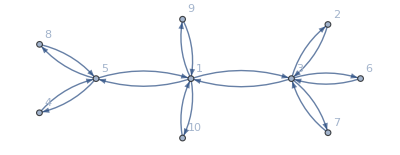

```mathematica
g=Graph[{1->3,1->5,1->9,1->10,2->3,3->1,3->2,3->6,3->7,4->5,5->1,5->4,5->8,6->3,7->3,8->5,9->1,10->1},VertexLabels->"Name"]
```

```mathematica
ConnectedComponents[g]
```

{{1,3,5,9,10,2,6,7,4,8}}

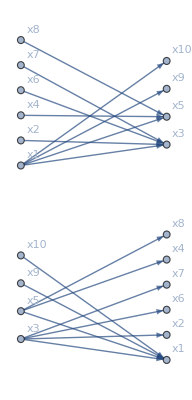

```mathematica
FromGraphToBipartite[g]
```

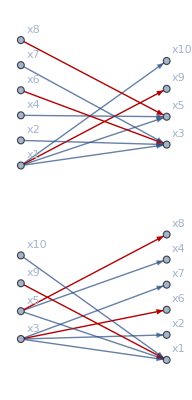

```mathematica
HighlightGraph[FromGraphToBipartite[g],FindIndependentEdgeSet[FromGraphToBipartite[g]],GraphLayout->"BipartiteEmbedding"]
```

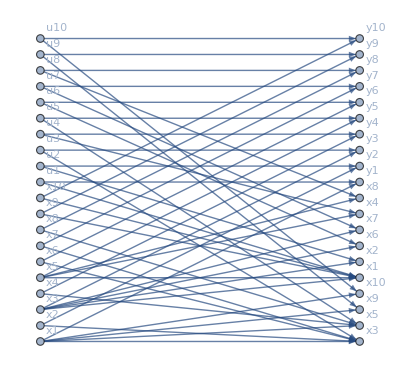

```mathematica
FromGraphToBipartiteInOut[g]
```

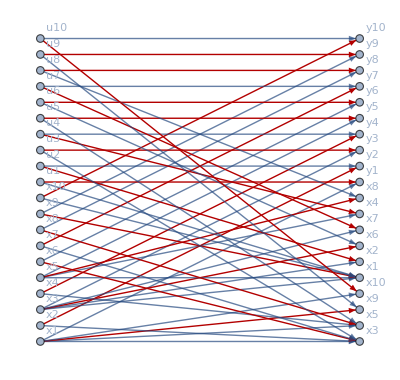

```mathematica
HighlightGraph[FromGraphToBipartiteInOut[g],FindIndependentEdgeSet[FromGraphToBipartiteInOut[g]],GraphLayout->"BipartiteEmbedding"]
```

```mathematica
ComputeSetsIandJ[g]
```

{{x10,x2,x7,x4},{x2,x4,x7,x10}}

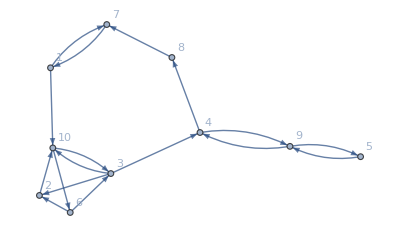
```mathematica
(* Paper Example 2 *)
g=-Graphics-
ConnectedComponents[g]
```

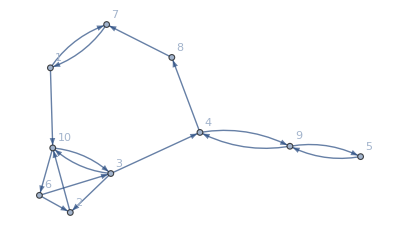

{{1,2,3,4,5,6,7,8,9,10}}

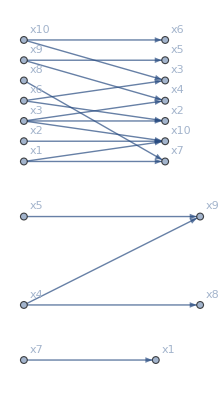

```mathematica
FromGraphToBipartite[g]
```

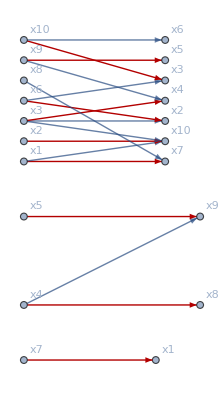

```mathematica
HighlightGraph[FromGraphToBipartite[g],FindIndependentEdgeSet[FromGraphToBipartite[g]],GraphLayout->"BipartiteEmbedding"]
```

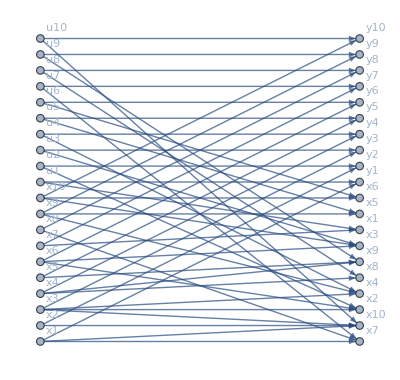

```mathematica
FromGraphToBipartiteInOut[g]
```

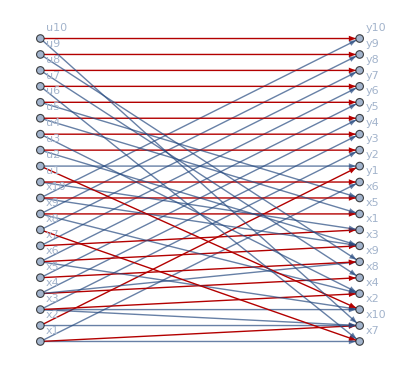

```mathematica
HighlightGraph[FromGraphToBipartiteInOut[g],FindIndependentEdgeSet[FromGraphToBipartiteInOut[g]],GraphLayout->"BipartiteEmbedding"]
```

```mathematica
ComputeSetsIandJ[g]
```

{{x2},{x2}}